```mathematica
PermulateMultiply[Srtst_,list1_,list2_]:=Srtst/.list1/.list2;
PrmltMltplExch[llset_]:=Exch[{llset[[1]],PermulateMultiply[llset[[1]],llset[[2]],llset[[3]]]}];
PrmltMltplExchPst[llset_]:={Exch[{llset[[1]],PermulateMultiply[llset[[1]],llset[[2]],llset[[3]]]}],llset[[4]],llset[[5]]};
Exch[list_]:=Module[{len=Length[list[[1]]],per={}},For[Exchi=1,Exchi≤Length[list[[1]]],Exchi++,If[list[[1,Exchi]]≠ list[[2,Exchi]],per=per∪{list[[1,Exchi]]->list[[2,Exchi]]}]];
per
]
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S4={51->57,57->59,59->53,53->51,54->58,58->56,56->52,52->54,11->31,31->27,27->47,47->11,17->37,37->21,21->41,41->17,14->34,34->24,24->44,44->14};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9={41->43,43->49,49->47,47->41,42->46,46->48,48->44,44->42,11->63,63->23,23->59,59->11,13->69,69->21,21->53,53->13,12->66,66->22,22->56,56->12};
StartSet={31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,11,12,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29};
IS1=Exch[{StartSet,StartSet/.S1/.S1/.S1}];
IS2=Exch[{StartSet,StartSet/.S2/.S2/.S2}];
IS3=Exch[{StartSet,StartSet/.S3/.S3/.S3}];
IS4=Exch[{StartSet,StartSet/.S4/.S4/.S4}];
IS5=Exch[{StartSet,StartSet/.S5/.S5/.S5}];
IS6=Exch[{StartSet,StartSet/.S6/.S6/.S6}];
IS7=Exch[{StartSet,StartSet/.S7/.S7/.S7}];
IS8=Exch[{StartSet,StartSet/.S8/.S8/.S8}];
IS9=Exch[{StartSet,StartSet/.S9/.S9/.S9}];
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
```

```mathematica
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};

S4={51->57,57->59,59->53,53->51,54->58,58->56,56->52,52->54,11->31,31->27,27->47,47->11,17->37,37->21,21->41,41->17,14->34,34->24,24->44,44->14};

S9={41->43,43->49,49->47,47->41,42->46,46->48,48->44,44->42,11->63,63->23,23->59,59->11,13->69,69->21,21->53,53->13,12->66,66->22,22->56,56->12};
```

```mathematica
TreePlot[Sl1∪Sl3∪Sl4∪Sl6∪Sl7∪Sl9,VertexLabeling->True,DirectedEdges-> True]
```

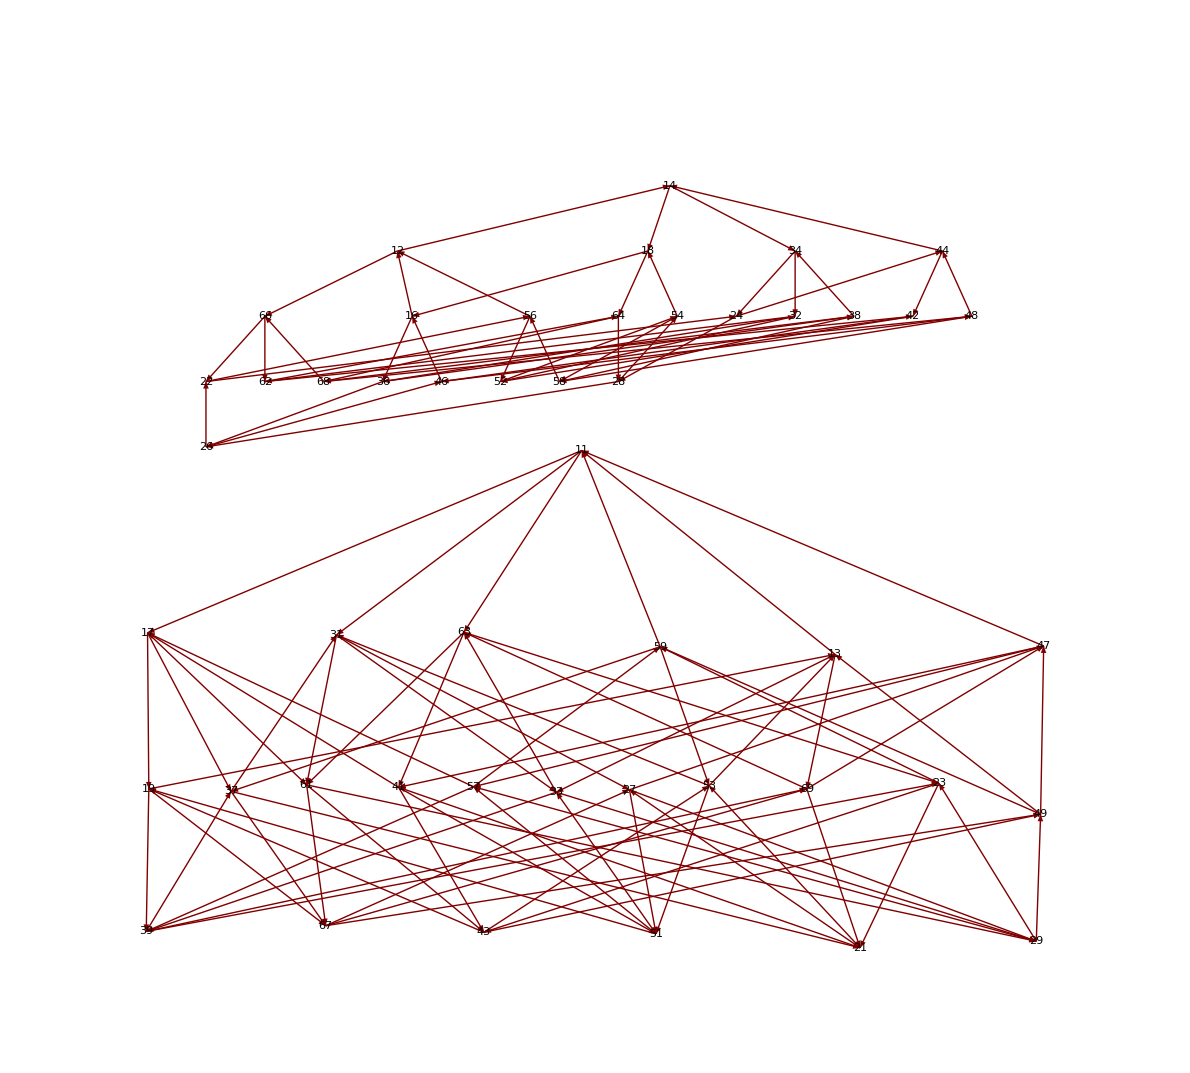

```mathematica
Exch[{StartSet,StartSet/.S9/.IS1/.IS6/.S1}](*S1S6^-1 S7S4*)
```

{12→68,13→67,21→23,22→56,23→59,26→36,29→63,36→12,39→13,42→26,43→29,44→66,46→48,47→69,48→44,49→47,56→46,59→49,63→39,64→42,66→22,67→43,68→64,69→21}

```mathematica
Exch[{StartSet,StartSet/.S1/.S4/.S7/.IS4}](*S4^-1 S7S4S1*)
Exch[{StartSet,StartSet/.S1/.S4/.IS3/.S9}](*S9S3^-1 S4S1*)
Exch[{StartSet,StartSet/.S1/.S7/.IS1/.IS4}](*S4^-1 S1^-1 S7S1*)
Exch[{StartSet,StartSet/.S1/.S7/.IS6/.IS9}](*S9^-1 S6^-1 S7S1*)
Exch[{StartSet,StartSet/.S9/.S1/.S4/.IS1}](*S1^-1 S4S1S9*)
Exch[{StartSet,StartSet/.S1/.IS4/.IS9/.S4}](*S4S9^-1 S4^-1 S1*)
Exch[{StartSet,StartSet/.S1/.IS7/.S4/.S9}](*S9S4S7^-1 S1*)
Exch[{StartSet,StartSet/.S1/.IS7/.IS3/.S4}](*S4S3^-1 S7^-1 S1*)
Exch[{StartSet,StartSet/.S4/.S7/.S1/.IS9}](*S9^-1 S1S7S4*)
Exch[{StartSet,StartSet/.S4/.S7/.IS6/.S1}](*S1S6^-1 S7S4*)
Exch[{StartSet,StartSet/.S4/.IS1/.IS4/.S9}](*S9S4^-1 S1^-1 S4*)
Exch[{StartSet,StartSet/.S4/.IS1/.S9/.S1}](*S1S9S1^-1 S4*)
```

{12→32,13→33,14→64,16→12,17→67,18→16,19→13,28→52,29→51,31→29,32→62,33→63,36→38,38→14,39→17,42→18,43→19,51→39,52→36,61→43,62→42,63→61,64→28,67→31}

{12→34,13→31,14→18,16→66,17→19,18→16,19→69,21→43,22→26,23→29,24→42,26→28,27→21,28→24,29→27,31→61,32→62,33→23,34→56,37→59,38→58,39→57,42→54,43→51,44→14,46→48,47→63,48→68,49→67,51→33,52→32,54→44,56→52,57→47,58→12,59→13,61→49,62→46,63→17,66→22,67→37,68→38,69→39}

{14→64,17→67,21→37,24→34,27→21,28→52,29→51,31→29,34→56,36→38,37→59,38→14,39→17,44→24,47→27,51→39,52→36,54→44,56→58,57→47,58→54,59→57,64→28,67→31}

{12→14,13→59,14→62,16→56,17→61,18→42,19→43,21→69,22→66,23→39,26→36,27→51,28→54,29→57,31→33,32→12,33→13,34→32,36→38,37→31,38→34,39→37,42→52,43→21,44→48,46→26,47→49,48→46,49→29,51→19,52→16,54→18,56→22,57→17,59→23,61→63,62→44,63→47,64→28,66→68,67→27,68→64,69→67}

{12→66,13→69,21→27,22→42,23→43,24→44,27→47,34→24,37→21,42→46,43→49,44→54,46→48,47→57,48→12,49→13,54→58,56→34,57→59,58→56,59→37,63→23,66→22,69→63}

{12→48,13→49,14→18,16→52,17→19,18→16,19→51,22→66,23→63,31→61,32→62,33→31,42→22,43→23,46→42,48→46,49→43,51→33,52→32,61→17,62→14,63→69,66→12,69→13}

{12→34,13→31,14→58,16→66,17→57,18→16,19→69,21→43,22→56,23→59,24→42,27→67,28→64,29→61,31→37,32→62,33→23,34→38,36→32,37→39,38→36,39→33,42→54,43→51,44→14,46→48,47→63,48→44,49→47,51→27,52→24,54→28,56→52,57→29,58→12,59→13,61→49,62→46,63→17,64→18,66→22,67→19,69→21}

{12→34,13→31,14→58,16→12,17→57,18→16,19→13,21→23,22→26,23→29,24→22,26→28,27→21,28→64,29→61,31→37,32→62,33→63,34→56,36→32,37→59,38→36,39→33,42→54,43→51,44→14,47→69,48→68,49→67,51→27,52→24,54→44,56→52,57→47,58→48,59→49,61→43,62→42,63→17,64→18,67→19,68→38,69→39}

{12→14,13→59,14→62,16→56,17→61,18→64,19→67,21→51,22→66,23→63,24→48,27→49,28→54,29→57,31→33,32→36,33→39,34→24,36→38,37→69,38→34,39→37,42→52,43→21,44→18,46→42,47→17,48→46,49→43,51→19,52→16,54→58,56→32,57→23,58→22,59→31,61→29,62→44,63→47,64→28,66→12,67→27,69→13}

{12→14,13→49,14→62,16→46,17→61,18→42,19→43,21→51,23→39,24→44,26→36,27→47,28→54,29→57,31→33,32→12,33→13,34→24,36→38,37→21,38→34,39→37,42→52,43→23,44→18,46→26,47→17,49→29,51→19,52→16,54→58,56→32,57→59,58→56,59→31,61→63,62→66,63→69,64→28,66→68,67→27,68→64,69→67}

{12→16,13→19,16→18,18→42,19→43,21→23,22→56,23→59,32→12,33→13,42→62,43→61,44→66,46→48,47→69,48→44,49→47,56→46,59→49,61→63,62→32,63→33,66→22,69→21}

{14→34,17→37,21→23,22→56,23→59,24→52,27→51,31→27,34→24,37→31,44→66,46→48,47→69,48→44,49→47,51→57,52→54,54→58,56→46,57→17,58→14,59→49,66→22,69→21}

```mathematica
S4^-1 S7 S4 S1
S9 S3^-1 S4 S1
S4^-1 S1^-1 S7 S1
```

```mathematica
S1,S4,S9

S2,S3,S5,S6,S7,S8(*保持11不动的完备系*)

S1, S2,S3,S5,S6,S7,S8,S7,S9
```

```mathematica
T1=Exch[{StartSet,StartSet/.S5/.S7/.IS6/.S8/.S3/.S5}](*S5S3S8S6^-1 S7S5*)
T2=Exch[{StartSet,StartSet/.S1/.S7/.IS1/.IS4}](*S4^-1 S1^-1 S7S1*)
T3=Exch[{StartSet,StartSet/.S4/.IS1/.S9/.S1}](*S1S9S1^-1 S4*)
```

{13→59,14→62,15→25,16→46,17→63,18→34,19→61,21→27,22→18,23→69,24→52,25→15,26→36,27→51,28→58,29→39,31→13,32→54,33→19,34→28,35→55,36→68,37→31,38→24,39→67,43→21,45→65,46→22,47→57,48→32,49→23,51→43,52→16,54→38,55→35,57→17,58→14,59→37,61→33,62→66,63→47,64→26,65→45,66→48,67→29,68→64,69→49}

{14→64,17→67,21→37,24→34,27→21,28→52,29→51,31→29,34→56,36→38,37→59,38→14,39→17,44→24,47→27,51→39,52→36,54→44,56→58,57→47,58→54,59→57,64→28,67→31}

{14→34,17→37,21→23,22→56,23→59,24→52,27→51,31→27,34→24,37→31,44→66,46→48,47→69,48→44,49→47,51→57,52→54,54→58,56→46,57→17,58→14,59→49,66→22,69→21}

```mathematica
TreePlot[Sl2∪Sl3∪Sl5∪Sl6∪Sl7∪Sl8,VertexLabeling->True,DirectedEdges-> True]
```

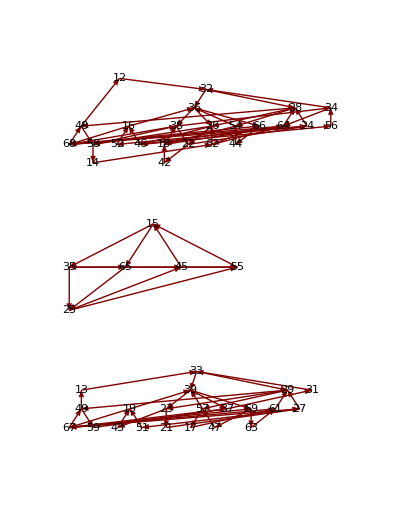

```mathematica
S2,S3,S5,S6,S7,S8(*保持11,41,53不动的完备系,12到任意位置*)

S5(*12动的唯一变换*)

S2,S3,T2=S4^-1 S1^-1 S7 S1,S6,S7,S8(*保持11,41,53,12,42不动的完备系，13任意*)
```

```mathematica
Tl2={{14->64,"T2"},{17->67,"T2"},{21->37,"T2"},{24->34,"T2"},{27->21,"T2"},{28->52,"T2"},{29->51,"T2"},{31->29,"T2"},{34->56,"T2"},{36->38,"T2"},{37->59,"T2"},{38->14,"T2"},{39->17,"T2"},{44->24,"T2"},{47->27,"T2"},{51->39,"T2"},{52->36,"T2"},{54->44,"T2"},{56->58,"T2"},{57->47,"T2"},{58->54,"T2"},{59->57,"T2"},{64->28,"T2"},{67->31,"T2"}};
```

```mathematica
TreePlot[Sl2∪Sl3∪Tl2∪Sl6∪Sl7∪Sl8,VertexLabeling->True,DirectedEdges-> True]
```

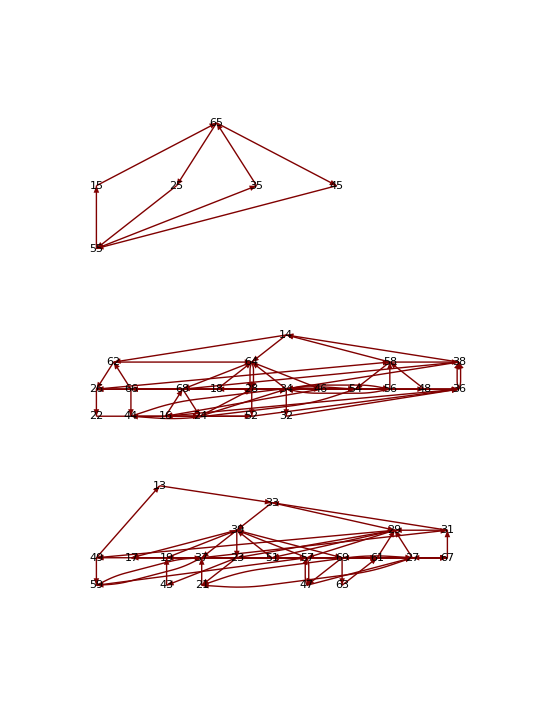

```mathematica
S2,S3,T2=S4^-1 S1^-1 S7 S1,S6,S7,S8(*保持11,41,53,12,42不动的完备系，13任意*)

S2,S3,T2=S4^-1 S1^-1 S7 S1,T3,S7,S8(*保持11,41,53,12,42,13,43,63不动的完备系，14任意*)
```

```mathematica
T3=Exch[{StartSet,StartSet/.S4/.IS1/.S9/.S1}](*S1S9S1^-1 S4*)
```

{14→34,17→37,21→23,22→56,23→59,24→52,27→51,31→27,34→24,37→31,44→66,46→48,47→69,48→44,49→47,51→57,52→54,54→58,56→46,57→17,58→14,59→49,66→22,69→21}

```mathematica
Tl3={{14->34,"T3"},{17->37,"T3"},{21->23,"T3"},{22->56,"T3"},{23->59,"T3"},{24->52,"T3"},{27->51,"T3"},{31->27,"T3"},{34->24,"T3"},{37->31,"T3"},{44->66,"T3"},{46->48,"T3"},{47->69,"T3"},{48->44,"T3"},{49->47,"T3"},{51->57,"T3"},{52->54,"T3"},{54->58,"T3"},{56->46,"T3"},{57->17,"T3"},{58->14,"T3"},{59->49,"T3"},{66->22,"T3"},{69->21,"T3"}};
```

```mathematica
TreePlot[Sl2∪Sl3∪Tl2∪Tl3∪Sl7∪Sl8,VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->1/2.]
```

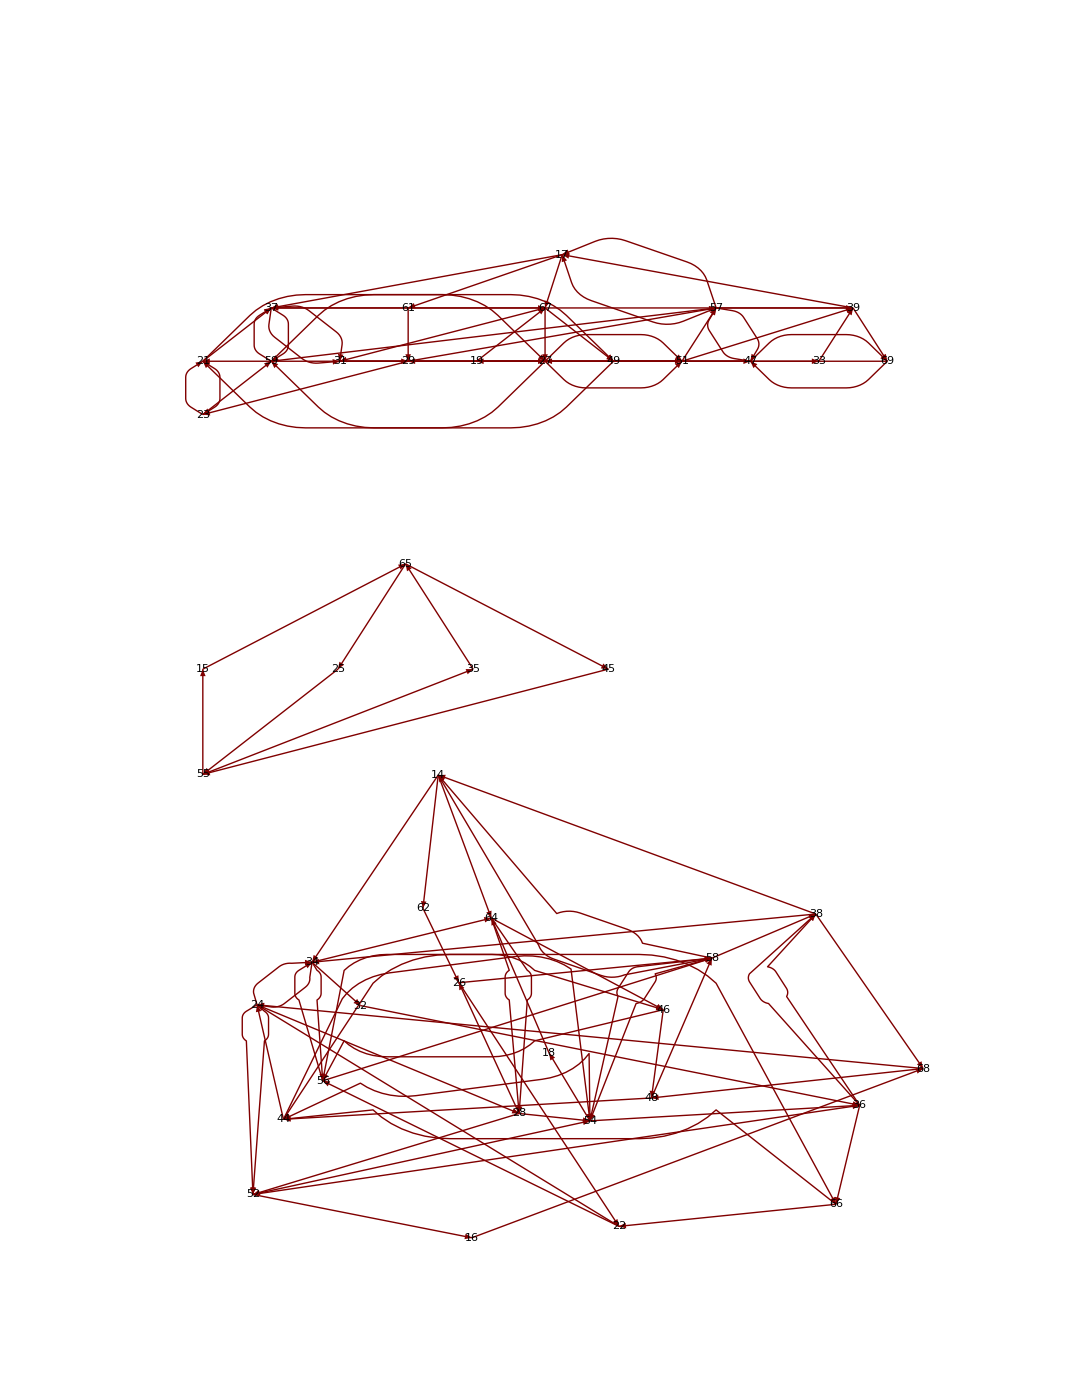

```mathematica
T4=Exch[{StartSet,StartSet/.IS8/.T3}](*T3S8^-1=S1 S9 S1^-1 S4 S8^-1*)
Exch[{StartSet,StartSet/.T3/.IS7/.T2}](*T2S7^-1 T3=S4^-1 S1^-1 S7 S1 S7^-1 S1 S9 S1^-1 S4*)
```

{15→55,16→54,17→37,21→23,22→56,23→59,24→68,25→65,26→62,27→51,31→27,34→24,37→31,44→66,46→48,47→69,48→44,49→47,51→57,54→58,55→25,56→46,57→17,58→26,59→49,62→34,65→15,66→22,68→16,69→21}

{18→44,19→39,21→23,22→58,23→57,24→36,27→21,29→61,32→56,33→29,36→32,37→59,39→33,44→66,46→48,47→69,48→24,49→27,56→46,57→47,58→64,59→49,61→67,64→18,66→22,67→19,69→37}

```mathematica
S2,S3,T2=S4^-1 S1^-1 S7 S1,T3=S1 S9 S1^-1 S4,S7,S8(*保持11,41,53,12,42,13,43,63不动的完备系，14任意*)

S2,S3,T4=S1 S9 S1^-1 S4 S8^-1,S7(*保持11,41,53,12,42,13,43,63,14,52不动的完备系，15到任意位置*)
```

```mathematica
Tl4={{15->55,"T4"},{16->54,"T4"},{17->37,"T4"},{21->23,"T4"},{22->56,"T4"},{23->59,"T4"},{24->68,"T4"},{25->65,"T4"},{26->62,"T4"},{27->51,"T4"},{31->27,"T4"},{34->24,"T4"},{37->31,"T4"},{44->66,"T4"},{46->48,"T4"},{47->69,"T4"},{48->44,"T4"},{49->47,"T4"},{51->57,"T4"},{54->58,"T4"},{55->25,"T4"},{56->46,"T4"},{57->17,"T4"},{58->26,"T4"},{59->49,"T4"},{62->34,"T4"},{65->15,"T4"},{66->22,"T4"},{68->16,"T4"},{69->21,"T4"}};
```

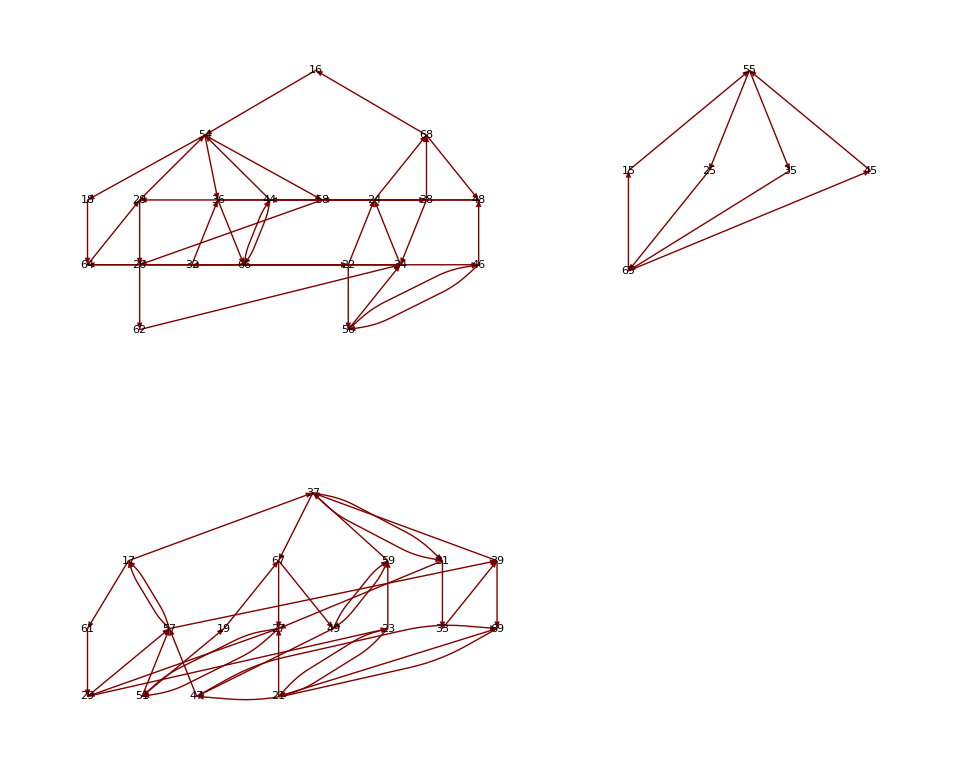

```mathematica
TreePlot[Sl2∪Sl3∪Sl7∪Tl4,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
S2,S3,T4=S1 S9 S1^-1 S4 S8^-1,S7(*保持11,41,53,12,42,13,43,63,14,52不动的完备系，15到任意位置*)

S2,S3,T5=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1,S7(*保持11,41,53,12,42,13,43,63,14,52,15,25不动的完备系,16到任意位置*)
```

```mathematica
T5=Exch[{StartSet,StartSet/.T4/.S2/.S2/.T4}];(*T4S2T4=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1*)
```

```mathematica
Table[{T5[[i]],"T5"},{i,Length[T5]}]//InputForm
```

{{16 -> 22, "T5"}, {17 -> 31, "T5"}, {21 -> 59, "T5"}, {22 -> 64, "T5"}, {23 -> 49, "T5"}, {24 -> 16, "T5"}, {26 -> 34, "T5"}, {27 -> 57, "T5"}, {31 -> 51, "T5"}, {34 -> 68, "T5"}, 
 {35 -> 45, "T5"}, {36 -> 66, "T5"}, {37 -> 27, "T5"}, {44 -> 58, "T5"}, {45 -> 35, "T5"}, {46 -> 44, "T5"}, {47 -> 21, "T5"}, {48 -> 36, "T5"}, {49 -> 69, "T5"}, {51 -> 17, "T5"}, 
 {54 -> 26, "T5"}, {55 -> 65, "T5"}, {56 -> 24, "T5"}, {57 -> 37, "T5"}, {58 -> 62, "T5"}, {59 -> 47, "T5"}, {62 -> 48, "T5"}, {64 -> 46, "T5"}, {65 -> 55, "T5"}, {66 -> 56, "T5"}, 
 {68 -> 54, "T5"}, {69 -> 23, "T5"}}

```mathematica
Tl5={{16->22,"T5"},{17->31,"T5"},{21->59,"T5"},{22->64,"T5"},{23->49,"T5"},{24->16,"T5"},{26->34,"T5"},{27->57,"T5"},{31->51,"T5"},{34->68,"T5"},{35->45,"T5"},{36->66,"T5"},{37->27,"T5"},{44->58,"T5"},{45->35,"T5"},{46->44,"T5"},{47->21,"T5"},{48->36,"T5"},{49->69,"T5"},{51->17,"T5"},{54->26,"T5"},{55->65,"T5"},{56->24,"T5"},{57->37,"T5"},{58->62,"T5"},{59->47,"T5"},{62->48,"T5"},{64->46,"T5"},{65->55,"T5"},{66->56,"T5"},{68->54,"T5"},{69->23,"T5"}};
```

```mathematica
{16,18,22,24,26,28,32,34,36,38,44,46,48,54,56,58,62,64,66,68}/.S2∪S3∪S7∪T5
```

{22,64,24,16,22,26,36,32,38,34,54,44,36,18,24,38,48,28,44,48}

```mathematica
{17,19,21,23,27,29,31,33,37,39,47,49,51,57,59,61,67,69}/.S2∪S3∪S7∪T5
```

{31,67,27,21,29,23,33,39,27,37,21,59,17,17,37,29,27,23}

```mathematica
TreePlot[Sl2∪Sl3∪Sl7∪Tl5,VertexLabeling->True,DirectedEdges-> True]
```

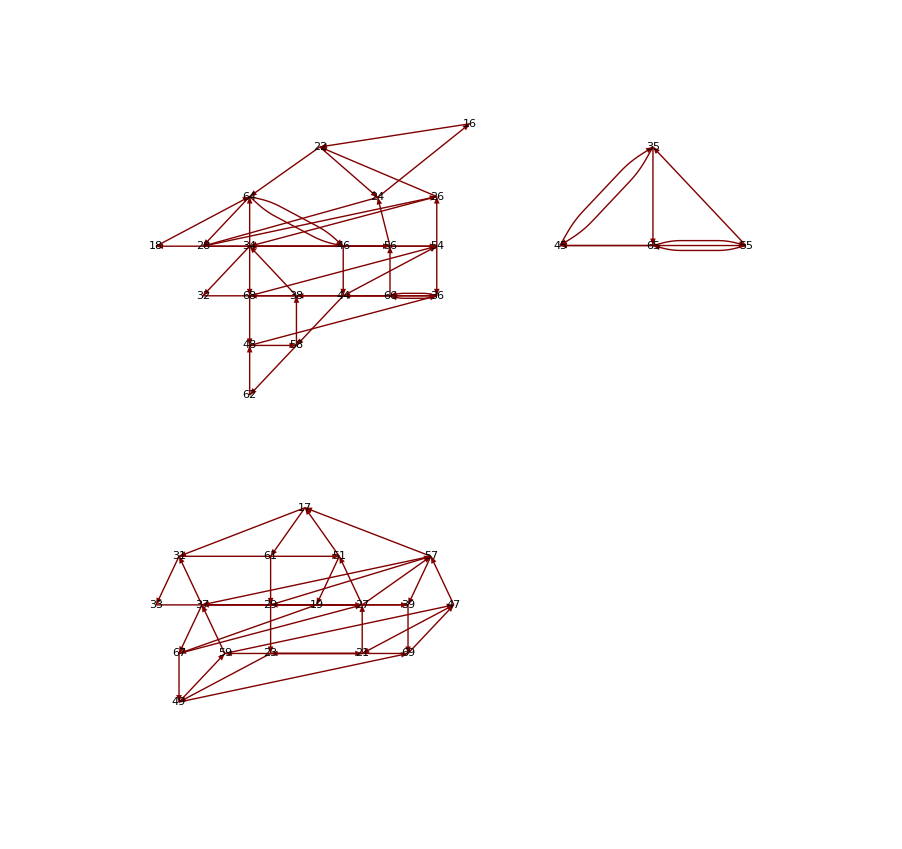

```mathematica
{18,22,24,26,28,32,34,36,38,44,46,48,54,56,58,64,66,68}/.S2∪S3∪S7∪T6
```

{64,24,22,22,26,36,32,38,34,38,56,58,18,28,38,28,24,26}

```mathematica
{17,19,21,23,27,29,31,33,37,39,47,49,51,57,59,61,67,69}/.S2∪S3∪S7∪T6
```

{51,67,27,21,29,23,17,39,29,23,57,21,19,17,37,29,27,47}

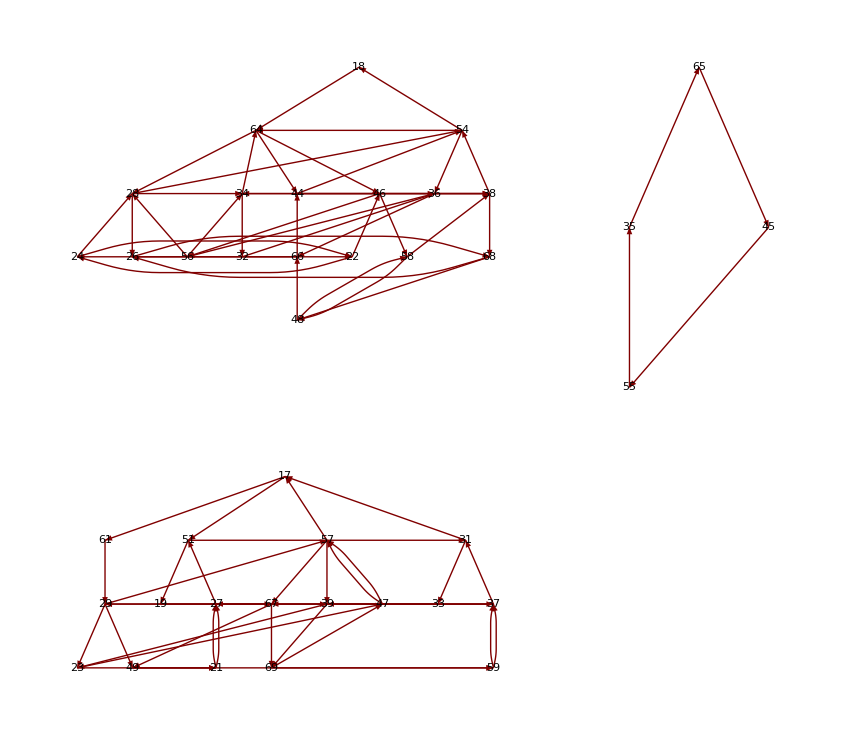

```mathematica
TreePlot[Sl2∪Sl3∪Sl7∪T6,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
T6=Exch[{StartSet,StartSet/.T5/.S3/.T5}](*T5 S3 T5=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1*)
```

{17→51,21→27,22→46,23→47,24→22,26→68,27→39,28→34,29→49,31→17,34→36,36→56,37→29,38→54,39→23,44→38,46→58,47→57,48→66,49→21,51→31,54→64,56→28,57→67,58→48,59→37,64→44,66→24,67→69,68→26,69→59}

```mathematica
Table[{T6[[i]],"T6"},{i,Length[T6]}]//InputForm
```

{{17 -> 51, "T6"}, {21 -> 27, "T6"}, {22 -> 46, "T6"}, {23 -> 47, "T6"}, {24 -> 22, "T6"}, {26 -> 68, "T6"}, {27 -> 39, "T6"}, {28 -> 34, "T6"}, {29 -> 49, "T6"}, {31 -> 17, "T6"}, 
 {34 -> 36, "T6"}, {36 -> 56, "T6"}, {37 -> 29, "T6"}, {38 -> 54, "T6"}, {39 -> 23, "T6"}, {44 -> 38, "T6"}, {46 -> 58, "T6"}, {47 -> 57, "T6"}, {48 -> 66, "T6"}, {49 -> 21, "T6"}, 
 {51 -> 31, "T6"}, {54 -> 64, "T6"}, {56 -> 28, "T6"}, {57 -> 67, "T6"}, {58 -> 48, "T6"}, {59 -> 37, "T6"}, {64 -> 44, "T6"}, {66 -> 24, "T6"}, {67 -> 69, "T6"}, {68 -> 26, "T6"}, 
 {69 -> 59, "T6"}}

```mathematica
Tl6={{17->51,"T6"},{21->27,"T6"},{22->46,"T6"},{23->47,"T6"},{24->22,"T6"},{26->68,"T6"},{27->39,"T6"},{28->34,"T6"},{29->49,"T6"},{31->17,"T6"},{34->36,"T6"},{36->56,"T6"},{37->29,"T6"},{38->54,"T6"},{39->23,"T6"},{44->38,"T6"},{46->58,"T6"},{47->57,"T6"},{48->66,"T6"},{49->21,"T6"},{51->31,"T6"},{54->64,"T6"},{56->28,"T6"},{57->67,"T6"},{58->48,"T6"},{59->37,"T6"},{64->44,"T6"},{66->24,"T6"},{67->69,"T6"},{68->26,"T6"},{69->59,"T6"}};
```

```mathematica
S2,S3,T5=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1,S7(*保持11,41,53,12,42,13,43,63,14,52,15,25不动的完备系,16到任意位置*)

S2,S3,T6=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1,S7(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62不动的完备系,17到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Sl7∪Tl6,VertexLabeling->True,DirectedEdges-> True]
```

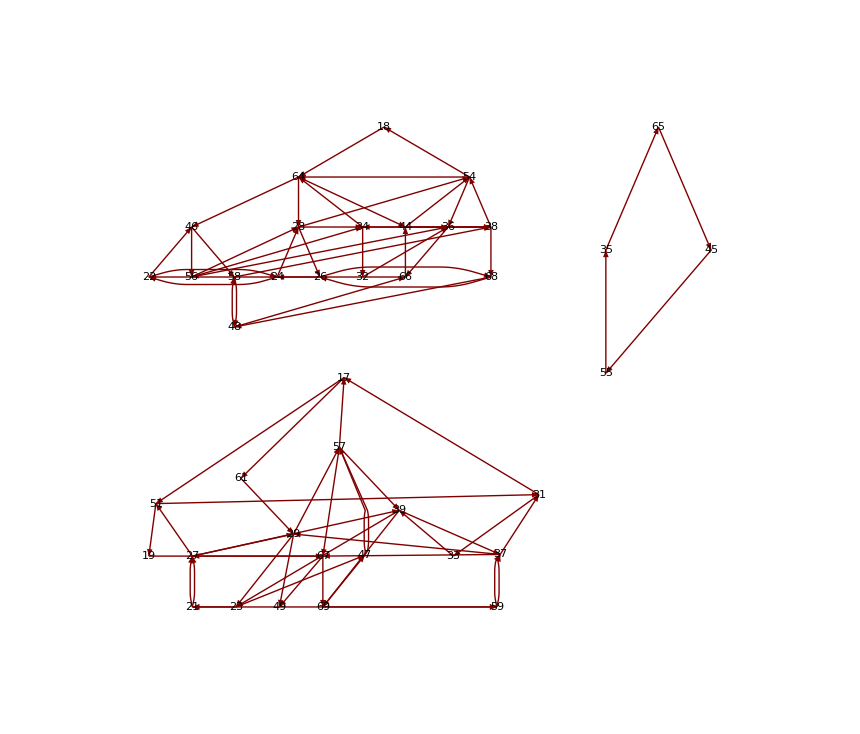

```mathematica
T7=Exch[{StartSet,StartSet/.IS7/.S3/.S7/.S7/.T6}](*T6 S7^2 S3 S7^-1=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1*)
```

{18→44,19→69,21→19,23→27,24→18,26→46,27→21,28→64,29→67,32→56,33→23,34→26,36→54,37→59,38→36,39→29,44→38,46→58,47→61,49→37,54→68,56→28,57→47,58→32,59→33,61→49,64→34,66→24,67→39,68→66,69→57}

```mathematica
Table[{T7[[i]],"T7"},{i,Length[T7]}]//InputForm
```

{{18 -> 44, "T7"}, {19 -> 69, "T7"}, {21 -> 19, "T7"}, {23 -> 27, "T7"}, {24 -> 18, "T7"}, {26 -> 46, "T7"}, {27 -> 21, "T7"}, {28 -> 64, "T7"}, {29 -> 67, "T7"}, {32 -> 56, "T7"}, 
 {33 -> 23, "T7"}, {34 -> 26, "T7"}, {36 -> 54, "T7"}, {37 -> 59, "T7"}, {38 -> 36, "T7"}, {39 -> 29, "T7"}, {44 -> 38, "T7"}, {46 -> 58, "T7"}, {47 -> 61, "T7"}, {49 -> 37, "T7"}, 
 {54 -> 68, "T7"}, {56 -> 28, "T7"}, {57 -> 47, "T7"}, {58 -> 32, "T7"}, {59 -> 33, "T7"}, {61 -> 49, "T7"}, {64 -> 34, "T7"}, {66 -> 24, "T7"}, {67 -> 39, "T7"}, {68 -> 66, "T7"}, 
 {69 -> 57, "T7"}}

```mathematica
Tl7={{18->44,"T7"},{19->69,"T7"},{21->19,"T7"},{23->27,"T7"},{24->18,"T7"},{26->46,"T7"},{27->21,"T7"},{28->64,"T7"},{29->67,"T7"},{32->56,"T7"},{33->23,"T7"},{34->26,"T7"},{36->54,"T7"},{37->59,"T7"},{38->36,"T7"},{39->29,"T7"},{44->38,"T7"},{46->58,"T7"},{47->61,"T7"},{49->37,"T7"},{54->68,"T7"},{56->28,"T7"},{57->47,"T7"},{58->32,"T7"},{59->33,"T7"},{61->49,"T7"},{64->34,"T7"},{66->24,"T7"},{67->39,"T7"},{68->66,"T7"},{69->57,"T7"}};
```

```mathematica
{18,22,24,26,28,32,34,36,38,44,46,48,54,56,58,64,66,68}/.S2∪S3∪T7
{19,21,23,27,29,33,37,39,47,49,57,59,61,67,69}/.S2∪S3∪T7
```

{44,24,18,22,26,56,26,54,36,38,56,58,36,28,32,34,24,48}

{69,19,21,21,23,23,59,29,57,37,39,33,49,39,47}

```mathematica
S2,S3,T6=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1,S7(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62不动的完备系,17到任意位置*)

S2,S3,T7=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51不动的完备系,18到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Tl7,VertexLabeling->True,DirectedEdges-> True]
```

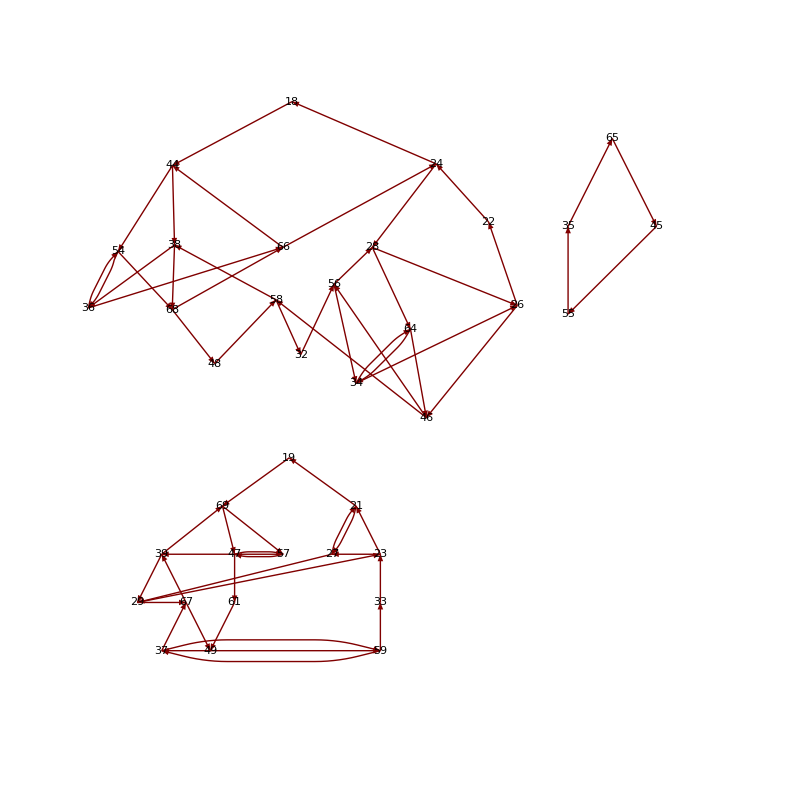

```mathematica
T8=Exch[{StartSet,StartSet/.T7/.IS2/.T7/.T7}](*T7^2 S2^-1 T7=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1*)
```

{19→47,21→57,23→19,24→38,27→69,28→46,33→21,34→58,35→55,37→23,38→66,44→54,45→65,46→56,47→37,49→33,54→24,55→45,56→34,57→49,58→28,59→27,61→59,65→35,66→44,69→61}

```mathematica
{18,22,24,26,28,32,34,36,38,44,46,48,54,56,58,64,66,68}/.S2∪S3∪T8
{19,21,23,27,29,33,37,39,47,49,57,59,61,67,69}/.S2∪S3∪T8
```

{18,24,28,22,26,32,58,66,66,54,56,58,24,34,28,46,44,48}

{47,27,19,29,23,21,23,69,37,33,39,27,59,49,47}

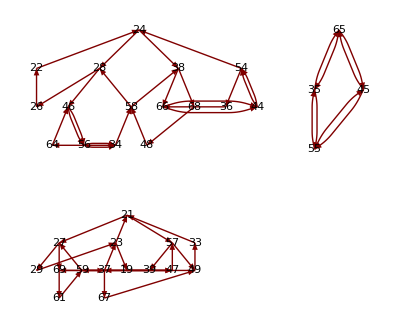

```mathematica
TreePlot[Sl2∪Sl3∪T8,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
S2,S3,T7=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51不动的完备系,18到任意位置*)

S2,S3,T8=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 ,A1=S6^-1 S3 S6(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32不动的完备系,19到任意位置*)
```

```mathematica
{22,24,26,28,34,36,38,44,46,48,54,56,58,64,66,68}/.S2∪S3∪T8∪A1
{19,21,23,27,29,33,37,39,47,49,57,59,61,67,69}/.S2∪S3∪T8∪A1
```

{24,28,22,26,58,22,64,54,56,58,24,34,28,46,44,48}

{47,27,19,29,23,21,23,21,37,33,19,27,29,47,47}

```mathematica
Table[{A1[[i]],"A1"},{i,Length[A1]}]//InputForm
```

{{19 -> 67, "A1"}, {21 -> 27, "A1"}, {22 -> 24, "A1"}, {24 -> 28, "A1"}, {27 -> 33, "A1"}, {28 -> 36, "A1"}, {29 -> 59, "A1"}, {33 -> 39, "A1"}, {36 -> 22, "A1"}, 
 {37 -> 61, "A1"}, {38 -> 64, "A1"}, {39 -> 21, "A1"}, {47 -> 57, "A1"}, {48 -> 58, "A1"}, {57 -> 19, "A1"}, {58 -> 38, "A1"}, {59 -> 37, "A1"}, {61 -> 29, "A1"}, 
 {64 -> 48, "A1"}, {67 -> 47, "A1"}}

```mathematica
Al1={{19->67,"A1"},{21->27,"A1"},{22->24,"A1"},{24->28,"A1"},{27->33,"A1"},{28->36,"A1"},{29->59,"A1"},{33->39,"A1"},{36->22,"A1"},{37->61,"A1"},{38->64,"A1"},{39->21,"A1"},{47->57,"A1"},{48->58,"A1"},{57->19,"A1"},{58->38,"A1"},{59->37,"A1"},{61->29,"A1"},{64->48,"A1"},{67->47,"A1"}};
```

```mathematica
Table[{T8[[i]],"T8"},{i,Length[T8]}]//InputForm
```

{{19 -> 47, "T8"}, {21 -> 57, "T8"}, {23 -> 19, "T8"}, {24 -> 38, "T8"}, {27 -> 69, "T8"}, {28 -> 46, "T8"}, {33 -> 21, "T8"}, {34 -> 58, "T8"}, {35 -> 55, "T8"}, {37 -> 23, "T8"}, 
 {38 -> 66, "T8"}, {44 -> 54, "T8"}, {45 -> 65, "T8"}, {46 -> 56, "T8"}, {47 -> 37, "T8"}, {49 -> 33, "T8"}, {54 -> 24, "T8"}, {55 -> 45, "T8"}, {56 -> 34, "T8"}, {57 -> 49, "T8"}, 
 {58 -> 28, "T8"}, {59 -> 27, "T8"}, {61 -> 59, "T8"}, {65 -> 35, "T8"}, {66 -> 44, "T8"}, {69 -> 61, "T8"}}

```mathematica
Tl8={{19->47,"T8"},{21->57,"T8"},{23->19,"T8"},{24->38,"T8"},{27->69,"T8"},{28->46,"T8"},{33->21,"T8"},{34->58,"T8"},{35->55,"T8"},{37->23,"T8"},{38->66,"T8"},{44->54,"T8"},{45->65,"T8"},{46->56,"T8"},{47->37,"T8"},{49->33,"T8"},{54->24,"T8"},{55->45,"T8"},{56->34,"T8"},{57->49,"T8"},{58->28,"T8"},{59->27,"T8"},{61->59,"T8"},{65->35,"T8"},{66->44,"T8"},{69->61,"T8"}}
```

{{19→47,T8},{21→57,T8},{23→19,T8},{24→38,T8},{27→69,T8},{28→46,T8},{33→21,T8},{34→58,T8},{35→55,T8},{37→23,T8},{38→66,T8},{44→54,T8},{45→65,T8},{46→56,T8},{47→37,T8},{49→33,T8},{54→24,T8},{55→45,T8},{56→34,T8},{57→49,T8},{58→28,T8},{59→27,T8},{61→59,T8},{65→35,T8},{66→44,T8},{69→61,T8}}

```mathematica
TreePlot[Sl2∪Sl3∪Tl8∪Al1,VertexLabeling->True,DirectedEdges-> True]
```

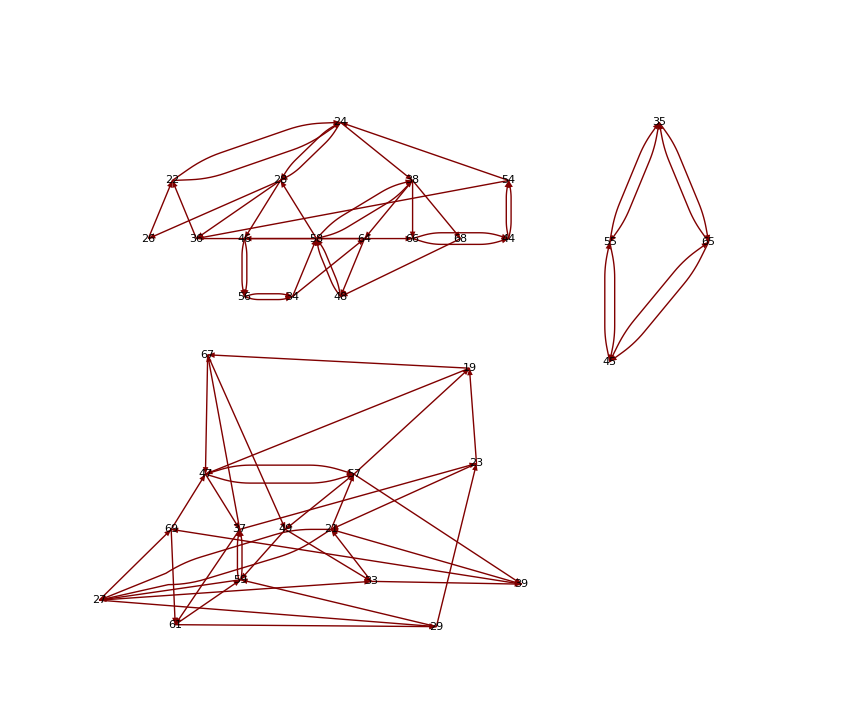

```mathematica
S2,S3,T8=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 ,A1=S6^-1 S3 S6(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32不动的完备系,19到任意位置*)
```

```mathematica
T8^20=e
T8^-1=S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1
```

```mathematica
IT8=Exch[{StartSet,StartSet/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8/.T8}]
```

{19→23,21→33,23→37,24→54,27→59,28→58,33→49,34→56,35→65,37→47,38→24,44→66,45→55,46→28,47→19,49→57,54→44,55→35,56→46,57→21,58→34,59→61,61→69,65→45,66→38,69→27}

```mathematica
R1=Exch[{StartSet,StartSet/.T8/.A1/.A1}](*A1^2 T8=S6^-1 S3^2 S6 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1*)
```

{21→67,22→28,23→47,24→48,27→69,28→46,29→37,34→64,35→55,36→24,37→23,38→66,39→27,44→54,45→65,46→56,47→29,48→38,49→21,54→36,55→45,56→34,57→49,58→22,59→39,64→58,65→35,66→44,67→57,69→59}

```mathematica
Table[{R1[[i]],"R1"},{i,Length[R1]}]//InputForm
```

{{21 -> 67, "R1"}, {22 -> 28, "R1"}, {23 -> 47, "R1"}, {24 -> 48, "R1"}, {27 -> 69, "R1"}, {28 -> 46, "R1"}, {29 -> 37, "R1"}, {34 -> 64, "R1"}, {35 -> 55, "R1"}, 
 {36 -> 24, "R1"}, {37 -> 23, "R1"}, {38 -> 66, "R1"}, {39 -> 27, "R1"}, {44 -> 54, "R1"}, {45 -> 65, "R1"}, {46 -> 56, "R1"}, {47 -> 29, "R1"}, {48 -> 38, "R1"}, 
 {49 -> 21, "R1"}, {54 -> 36, "R1"}, {55 -> 45, "R1"}, {56 -> 34, "R1"}, {57 -> 49, "R1"}, {58 -> 22, "R1"}, {59 -> 39, "R1"}, {64 -> 58, "R1"}, {65 -> 35, "R1"}, 
 {66 -> 44, "R1"}, {67 -> 57, "R1"}, {69 -> 59, "R1"}}

```mathematica
Rl1={{21->67,"R1"},{22->28,"R1"},{23->47,"R1"},{24->48,"R1"},{27->69,"R1"},{28->46,"R1"},{29->37,"R1"},{34->64,"R1"},{35->55,"R1"},{36->24,"R1"},{37->23,"R1"},{38->66,"R1"},{39->27,"R1"},{44->54,"R1"},{45->65,"R1"},{46->56,"R1"},{47->29,"R1"},{48->38,"R1"},{49->21,"R1"},{54->36,"R1"},{55->45,"R1"},{56->34,"R1"},{57->49,"R1"},{58->22,"R1"},{59->39,"R1"},{64->58,"R1"},{65->35,"R1"},{66->44,"R1"},{67->57,"R1"},{69->59,"R1"}};
```

```mathematica
T9=Exch[{StartSet,StartSet/.T8/.S3/.IT8/.IS3/.T8}](*T8 S3^-1 T8^-1 S3T8=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1*)
T10=Exch[{StartSet,StartSet/.S6/.S9/.IS3/.IS9/.S3/.IS6}](*S6^-1 S3 S9^-1 S3^-1 S9 S6*)
```

{21→49,22→24,23→29,24→66,27→47,28→38,29→27,34→22,35→55,37→21,38→28,39→57,44→54,45→65,46→56,47→23,48→58,49→67,54→48,55→45,56→34,57→59,58→46,59→69,65→35,66→44,67→37,69→39}

{21→27,22→24,23→29,24→68,26→48,27→47,29→49,37→21,39→23,47→57,48→58,49→67,57→59,58→26,59→37,67→69,68→22,69→39}

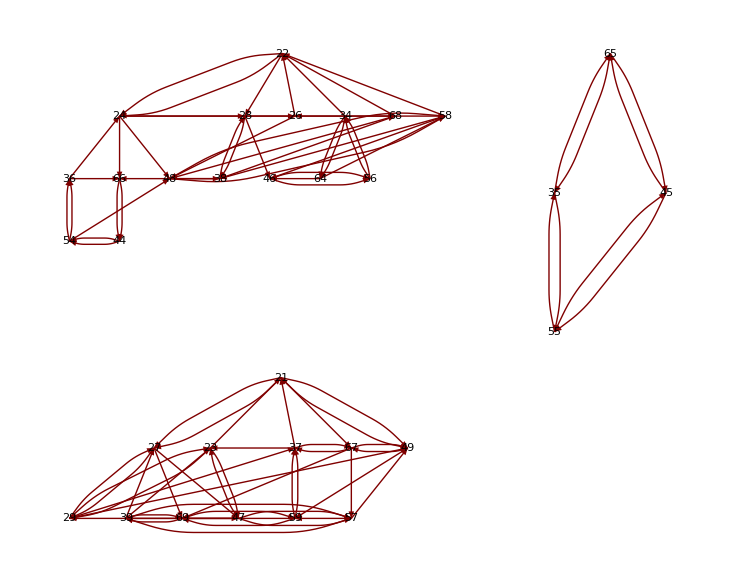

```mathematica
TreePlot[Sl2∪Sl3∪T9∪T10∪R1,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
{22,24,26,28,34,36,38,44,46,48,54,56,58,64,66,68}/.S2∪S3∪T9∪T10∪R1
{21,23,27,29,37,39,47,49,57,59,67,69}/.S2∪S3∪T9∪T10∪R1
```

{24,28,22,26,22,24,28,54,56,38,36,34,22,46,44,22}

{27,21,29,23,21,23,23,21,39,37,37,39}

```mathematica
S2,S3,T8=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 (*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32不动的完备系,19到任意位置*)

S2,S3,T9=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 ,
T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,
R1=S6^-1 S3^2 S6 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61不动的完备系,34到任意位置*)
```

```mathematica
Table[{T10[[i]],"T10"},{i,Length[T10]}]//InputForm
```

{{21 -> 27, "T10"}, {22 -> 24, "T10"}, {23 -> 29, "T10"}, {24 -> 68, "T10"}, {26 -> 48, "T10"}, {27 -> 47, "T10"}, {29 -> 49, "T10"}, {37 -> 21, "T10"}, {39 -> 23, "T10"}, 
 {47 -> 57, "T10"}, {48 -> 58, "T10"}, {49 -> 67, "T10"}, {57 -> 59, "T10"}, {58 -> 26, "T10"}, {59 -> 37, "T10"}, {67 -> 69, "T10"}, {68 -> 22, "T10"}, {69 -> 39, "T10"}}

```mathematica
Tl9={{21->49,"T9"},{22->24,"T9"},{23->29,"T9"},{24->66,"T9"},{27->47,"T9"},{28->38,"T9"},{29->27,"T9"},{34->22,"T9"},{35->55,"T9"},{37->21,"T9"},{38->28,"T9"},{39->57,"T9"},{44->54,"T9"},{45->65,"T9"},{46->56,"T9"},{47->23,"T9"},{48->58,"T9"},{49->67,"T9"},{54->48,"T9"},{55->45,"T9"},{56->34,"T9"},{57->59,"T9"},{58->46,"T9"},{59->69,"T9"},{65->35,"T9"},{66->44,"T9"},{67->37,"T9"},{69->39,"T9"}};
Tl10={{21->27,"T10"},{22->24,"T10"},{23->29,"T10"},{24->68,"T10"},{26->48,"T10"},{27->47,"T10"},{29->49,"T10"},{37->21,"T10"},{39->23,"T10"},{47->57,"T10"},{48->58,"T10"},{49->67,"T10"},{57->59,"T10"},{58->26,"T10"},{59->37,"T10"},{67->69,"T10"},{68->22,"T10"},{69->39,"T10"}};
```

```mathematica
TreePlot[Sl2∪Sl3∪Tl9∪Tl10∪Rl1,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
R2=Exch[{StartSet,StartSet/.R1/.IS2}](*R1 S2^-1*)
```

{21→67,22→28,23→47,24→48,27→69,28→64,29→37,35→45,36→24,37→23,38→36,39→27,45→35,47→29,48→38,49→21,55→65,57→49,58→22,59→39,64→58,65→55,67→57,69→59}

```mathematica
Table[{R2[[i]],"R2"},{i,Length[R2]}]//InputForm
```

{{21 -> 59, "R2"}, {22 -> 48, "R2"}, {23 -> 49, "R2"}, {27 -> 57, "R2"}, {28 -> 38, "R2"}, {29 -> 39, "R2"}, {35 -> 45, "R2"}, {36 -> 66, "R2"}, {37 -> 27, "R2"}, {38 -> 28, "R2"}, 
 {39 -> 67, "R2"}, {44 -> 36, "R2"}, {45 -> 35, "R2"}, {46 -> 56, "R2"}, {47 -> 21, "R2"}, {48 -> 22, "R2"}, {49 -> 69, "R2"}, {55 -> 65, "R2"}, {56 -> 64, "R2"}, {57 -> 37, "R2"}, 
 {59 -> 47, "R2"}, {64 -> 46, "R2"}, {65 -> 55, "R2"}, {66 -> 44, "R2"}, {67 -> 29, "R2"}, {69 -> 23, "R2"}}

```mathematica
Rl2={{21->59,"R2"},{22->48,"R2"},{23->49,"R2"},{27->57,"R2"},{28->38,"R2"},{29->39,"R2"},{35->45,"R2"},{36->66,"R2"},{37->27,"R2"},{38->28,"R2"},{39->67,"R2"},{44->36,"R2"},{45->35,"R2"},{46->56,"R2"},{47->21,"R2"},{48->22,"R2"},{49->69,"R2"},{55->65,"R2"},{56->64,"R2"},{57->37,"R2"},{59->47,"R2"},{64->46,"R2"},{65->55,"R2"},{66->44,"R2"},{67->29,"R2"},{69->23,"R2"}};
```

```mathematica
T11=Exch[{StartSet,StartSet/.IS2/.T9}](*T9 S2^-1=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1*)
T12=Exch[{StartSet,StartSet/.IS4/.IS5/.IS6/.S1/.S1/.S2/.S2/.S3/.S3/.S5/.IS3/.IS5/.S3/.S3/.S5/.IS3/.IS5/.S1/.S1/.S2/.S2/.S3/.S3/.S4/.S5/.S6}](*S4 S5 S6 S1^2 S2^2 S3^2 S2^-1 S5^2 S2 S5^2 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1*)
```

{21→49,22→24,23→29,24→66,27→47,28→38,29→27,35→45,36→48,37→21,38→28,39→57,45→35,46→64,47→23,48→58,49→67,55→65,57→59,58→46,59→69,64→22,65→55,66→36,67→37,69→39}

{22→44,44→46,46→22,48→56,56→66,66→48}

```mathematica
Table[{T12[[i]],"T12"},{i,Length[T12]}]//InputForm
```

{{22 -> 44, "T12"}, {44 -> 46, "T12"}, {46 -> 22, "T12"}, {48 -> 56, "T12"}, {56 -> 66, "T12"}, {66 -> 48, "T12"}}

```mathematica
Tl11={{21->49,"T11"},{22->24,"T11"},{23->29,"T11"},{24->66,"T11"},{27->47,"T11"},{28->38,"T11"},{29->27,"T11"},{35->45,"T11"},{36->48,"T11"},{37->21,"T11"},{38->28,"T11"},{39->57,"T11"},{45->35,"T11"},{46->64,"T11"},{47->23,"T11"},{48->58,"T11"},{49->67,"T11"},{55->65,"T11"},{57->59,"T11"},{58->46,"T11"},{59->69,"T11"},{64->22,"T11"},{65->55,"T11"},{66->36,"T11"},{67->37,"T11"},{69->39,"T11"}};
Tl12={{22->44,"T12"},{44->46,"T12"},{46->22,"T12"},{48->56,"T12"},{56->66,"T12"},{66->48,"T12"}};
```

```mathematica
{22,24,26,28,36,38,44,46,48,56,58,64,66,68}/.S3∪T10∪T11∪T12
{21,23,27,29,37,39,47,49,57,59,67,69}/.S3∪T10∪T11∪T12
```

{24,28,22,26,48,28,46,22,56,66,26,22,36,22}

{27,21,29,23,21,23,23,59,39,37,37,39}

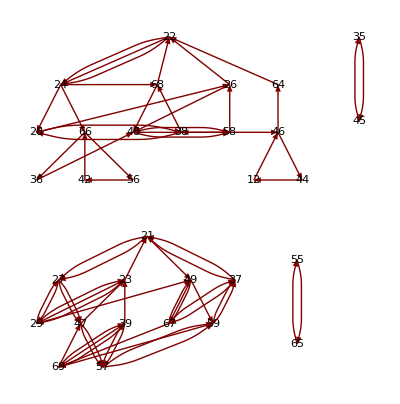

```mathematica
TreePlot[Sl3∪Tl10∪T11∪T12,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
S2,S3,T9=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 ,
T10=S6^-1 S3 S9^-1 S3^-1 S9 S6
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61不动的完备系,34到任意位置*)

S3,T11=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 ,
T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,T12=S4 S5 S6 S1^2 S2^2 S3^2 S2^-1 S5^2 S2 S5^2 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54不动的完备系,36到任意位置*)
```

```mathematica
TreePlot[Sl3∪Tl10∪Tl11∪Tl12,VertexLabeling->True,DirectedEdges-> True]
```

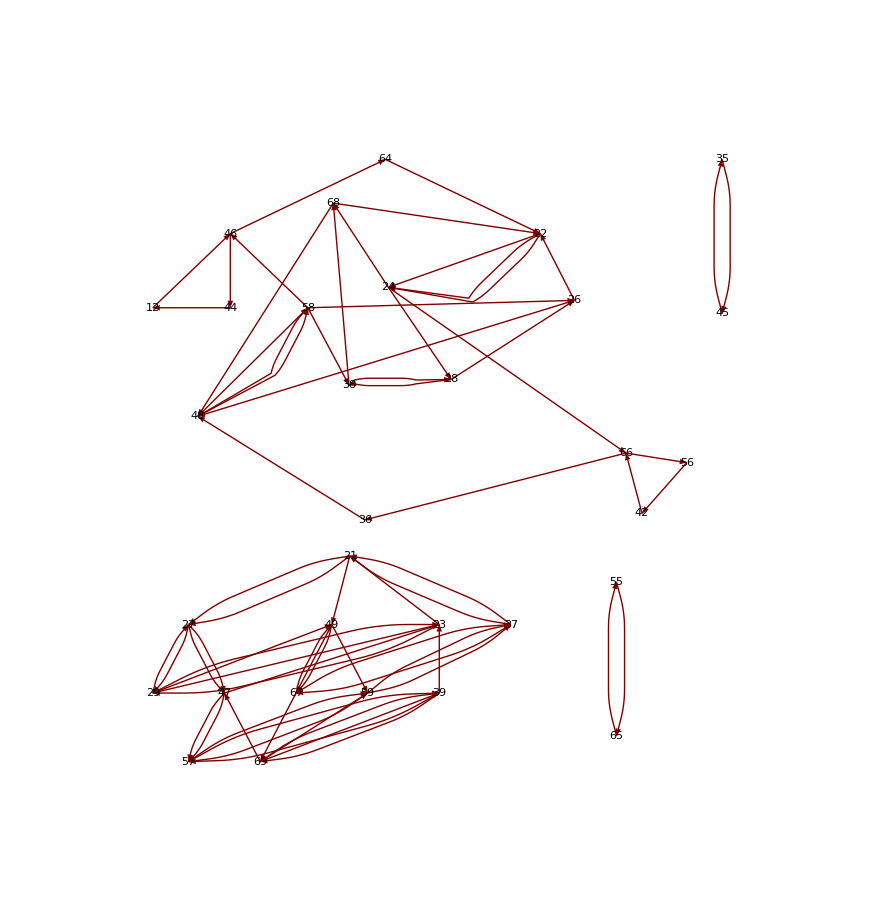

```mathematica
T13=Exch[{StartSet,StartSet/.T11/.S3/.S3/.T11/.IS3/.T11/.T11}](*T11^2 S3^-1 T11 S3^2 T11=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1*)
```

{21→27,22→28,23→21,24→58,26→48,27→29,28→46,29→23,37→67,38→66,39→69,46→26,47→57,48→38,49→59,57→39,58→24,59→37,66→68,67→49,68→22,69→47}

```mathematica
Table[{T13[[i]],"T13"},{i,Length[T13]}]//InputForm
```

{{21 -> 27, "T13"}, {22 -> 28, "T13"}, {23 -> 21, "T13"}, {24 -> 58, "T13"}, {26 -> 48, "T13"}, {27 -> 29, "T13"}, {28 -> 46, "T13"}, {29 -> 23, "T13"}, {37 -> 67, "T13"}, 
 {38 -> 66, "T13"}, {39 -> 69, "T13"}, {46 -> 26, "T13"}, {47 -> 57, "T13"}, {48 -> 38, "T13"}, {49 -> 59, "T13"}, {57 -> 39, "T13"}, {58 -> 24, "T13"}, {59 -> 37, "T13"}, 
 {66 -> 68, "T13"}, {67 -> 49, "T13"}, {68 -> 22, "T13"}, {69 -> 47, "T13"}}

```mathematica
Tl13={{21->27,"T13"},{22->28,"T13"},{23->21,"T13"},{24->58,"T13"},{26->48,"T13"},{27->29,"T13"},{28->46,"T13"},{29->23,"T13"},{37->67,"T13"},{38->66,"T13"},{39->69,"T13"},{46->26,"T13"},{47->57,"T13"},{48->38,"T13"},{49->59,"T13"},{57->39,"T13"},{58->24,"T13"},{59->37,"T13"},{66->68,"T13"},{67->49,"T13"},{68->22,"T13"},{69->47,"T13"}};
```

```mathematica
{22,24,26,28,38,44,46,48,56,58,66,68}/.S3∪T10∪T12∪T13
{21,23,27,29,37,39,47,49,57,59,67,69}/.S3∪T10∪T12∪T13
```

{24,28,22,26,66,46,22,38,66,24,48,22}

{27,21,29,23,21,23,57,59,39,37,49,39}

```mathematica
S3,T11=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 ,
T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,T12=S4 S5 S6 S1^2 S2^2 S3^2 S2^-1 S5^2 S2 S5^2 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54不动的完备系,36到任意位置*)

S3,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,T12=S4 S5 S6 S1^2 S2^2 S3^2 S2^-1 S5^2 S2 S5^2 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1,
T13=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64不动的完备系,44到任意位置*)
```

```mathematica
TreePlot[Sl3∪Tl10∪Tl12∪Tl13,VertexLabeling->True,DirectedEdges-> True]
```

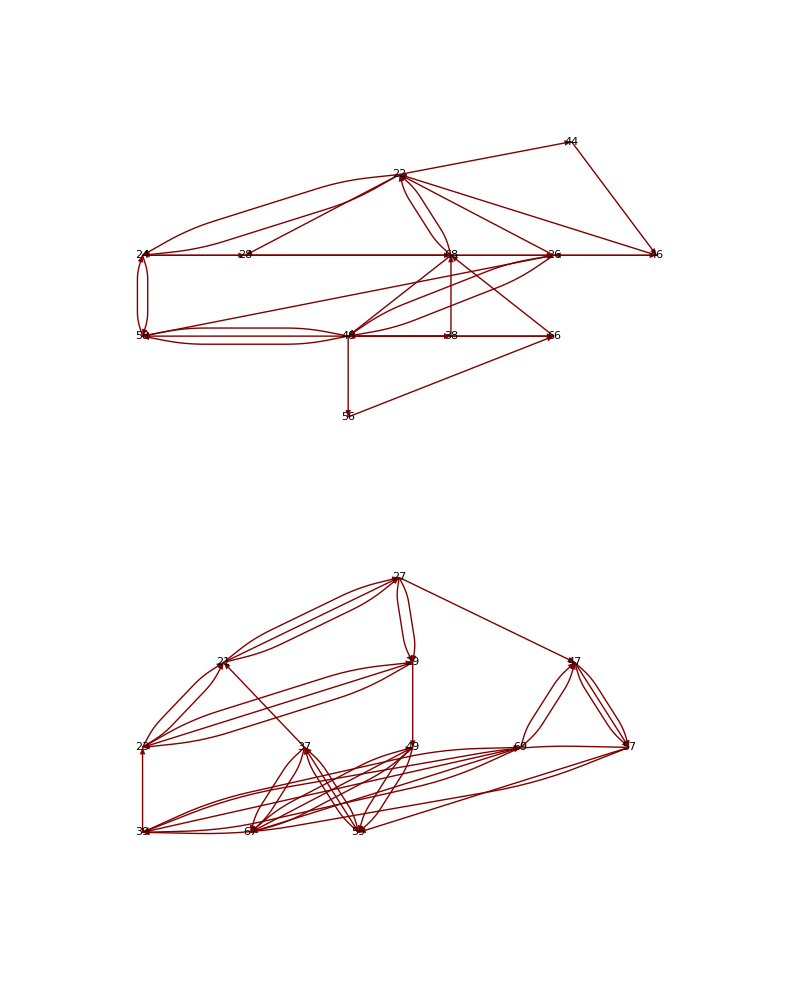

```mathematica
T14=Exch[{StartSet,StartSet/.T12/.T12/.T12}]
```

{}

```mathematica
{22,24,26,28,38,46,48,58,66,68}/.S3∪T10∪T13
{21,23,27,29,37,39,47,49,57,59,67,69}/.S3∪T10∪T13
```

{24,28,22,26,66,26,38,24,68,22}

{27,21,29,23,21,23,57,59,39,37,49,39}

```mathematica
S3,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,T12=S4 S5 S6 S1^2 S2^2 S3^2 S2^-1 S5^2 S2 S5^2 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1,
T13=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64不动的完备系,44到任意位置*)

S3,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,
T13=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56不动的完备系,46到任意位置*)
```

```mathematica
TreePlot[Sl3∪Tl10∪Tl13,VertexLabeling->True,DirectedEdges-> True]
```

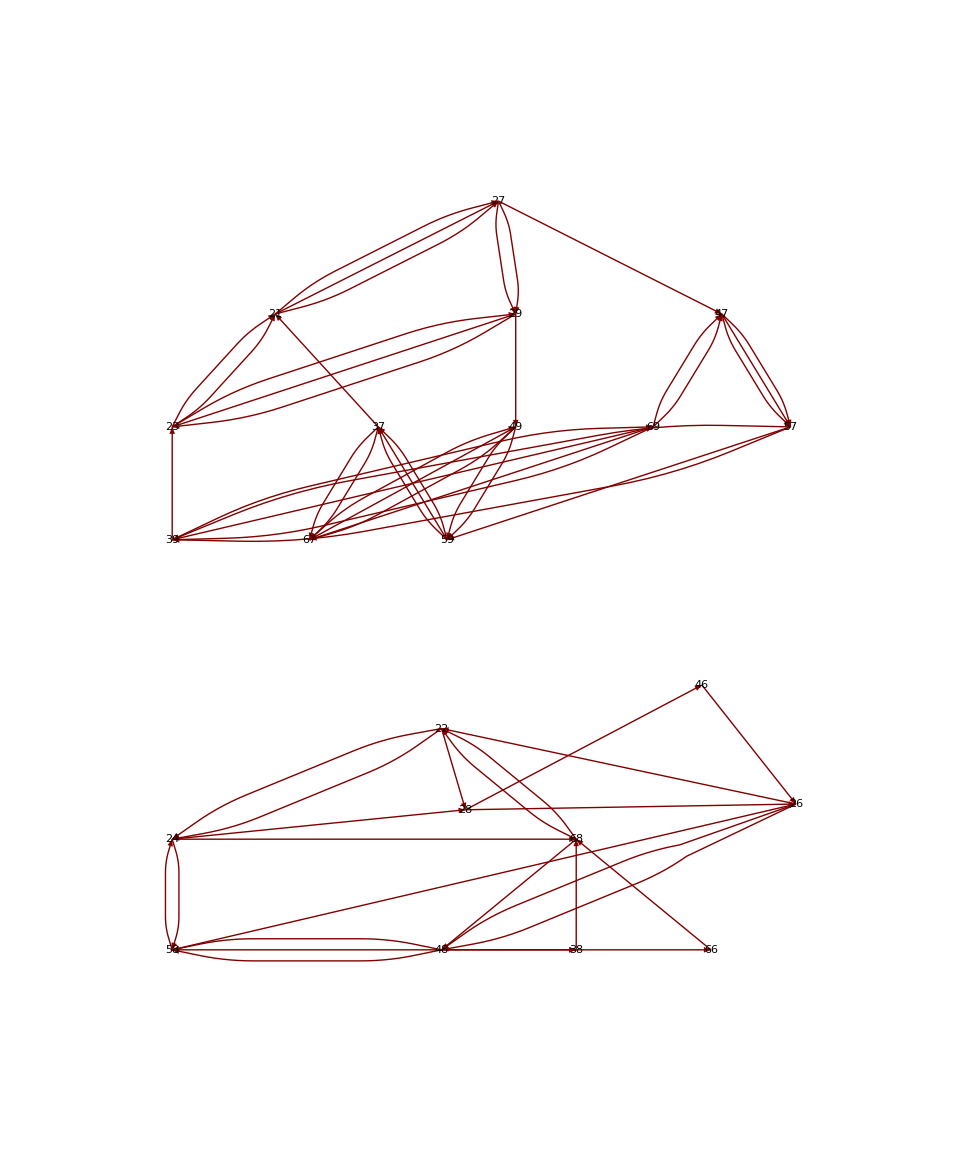

```mathematica
T14=Exch[{StartSet,StartSet/.T13/.IS3/.T13}]
```

{21→27,22→58,23→21,24→38,26→22,27→29,28→26,29→23,37→67,38→68,39→69,47→57,48→24,49→59,57→39,58→28,59→37,67→49,68→48,69→47}

```mathematica
Table[{T16[[i]],"T16"},{i,Length[T16]}]//InputForm
```

{{21 -> 39, "T16"}, {22 -> 26, "T16"}, {23 -> 27, "T16"}, {24 -> 22, "T16"}, {26 -> 24, "T16"}, {27 -> 69, "T16"}, {29 -> 47, "T16"}, {37 -> 23, "T16"}, {39 -> 59, "T16"}, 
 {47 -> 67, "T16"}, {48 -> 68, "T16"}, {49 -> 37, "T16"}, {57 -> 49, "T16"}, {58 -> 48, "T16"}, {59 -> 29, "T16"}, {67 -> 21, "T16"}, {68 -> 58, "T16"}, {69 -> 57, "T16"}}

```mathematica
Tl14={{21->27,"T14"},{22->58,"T14"},{23->21,"T14"},{24->38,"T14"},{26->22,"T14"},{27->29,"T14"},{28->26,"T14"},{29->23,"T14"},{37->67,"T14"},{38->68,"T14"},{39->69,"T14"},{47->57,"T14"},{48->24,"T14"},{49->59,"T14"},{57->39,"T14"},{58->28,"T14"},{59->37,"T14"},{67->49,"T14"},{68->48,"T14"},{69->47,"T14"}};
```

```mathematica
T15=Exch[{StartSet,StartSet/.S6/.S9/.IS3/.IS9/.S3/.IS6}](*S6^-1 S3 S9^-1 S3^-1 S9 S6*)
```

{21→27,22→24,23→29,24→68,26→48,27→47,29→49,37→21,39→23,47→57,48→58,49→67,57→59,58→26,59→37,67→69,68→22,69→39}

```mathematica
Tl15={{21->27,"T15"},{22->24,"T15"},{23->29,"T15"},{24->68,"T15"},{26->48,"T15"},{27->47,"T15"},{29->49,"T15"},{37->21,"T15"},{39->23,"T15"},{47->57,"T15"},{48->58,"T15"},{49->67,"T15"},{57->59,"T15"},{58->26,"T15"},{59->37,"T15"},{67->69,"T15"},{68->22,"T15"},{69->39,"T15"}};
```

```mathematica
T16=Exch[{StartSet,StartSet/.S6/.S3/.S3/.IS6/.S3/.S6/.S3/.IS6}](*S6^-1 S3 S6 S3 S6^-1 S3^2 S6*)
```

{21→39,22→26,23→27,24→22,26→24,27→69,29→47,37→23,39→59,47→67,48→68,49→37,57→49,58→48,59→29,67→21,68→58,69→57}

```mathematica
Tl16={{21->39,"T16"},{22->26,"T16"},{23->27,"T16"},{24->22,"T16"},{26->24,"T16"},{27->69,"T16"},{29->47,"T16"},{37->23,"T16"},{39->59,"T16"},{47->67,"T16"},{48->68,"T16"},{49->37,"T16"},{57->49,"T16"},{58->48,"T16"},{59->29,"T16"},{67->21,"T16"},{68->58,"T16"},{69->57,"T16"}};
```

```mathematica
{22,24,26,28,38,48,58,68}/.S3∪T10∪T14∪T15∪T16
{21,23,27,29,37,39,47,49,57,59,67,69}/.S3∪T10∪T14∪T15∪T16
```

{24,22,22,26,68,24,26,22}

{27,21,29,23,21,23,57,37,39,29,21,39}

```mathematica
S3,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,
T13=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56不动的完备系,46到任意位置*)

S3,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,
T14=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1,
T15=S6^-1 S3 S9^-1 S3^-1 S9 S6,T16=S6^-1 S3 S6 S3 S6^-1 S3^2 S6
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66不动的完备系,21到任意位置*)
```

```mathematica
TreePlot[Sl3∪Tl10∪Tl14∪Tl15∪Tl16,Top,VertexLabeling->True,DirectedEdges-> True]
```

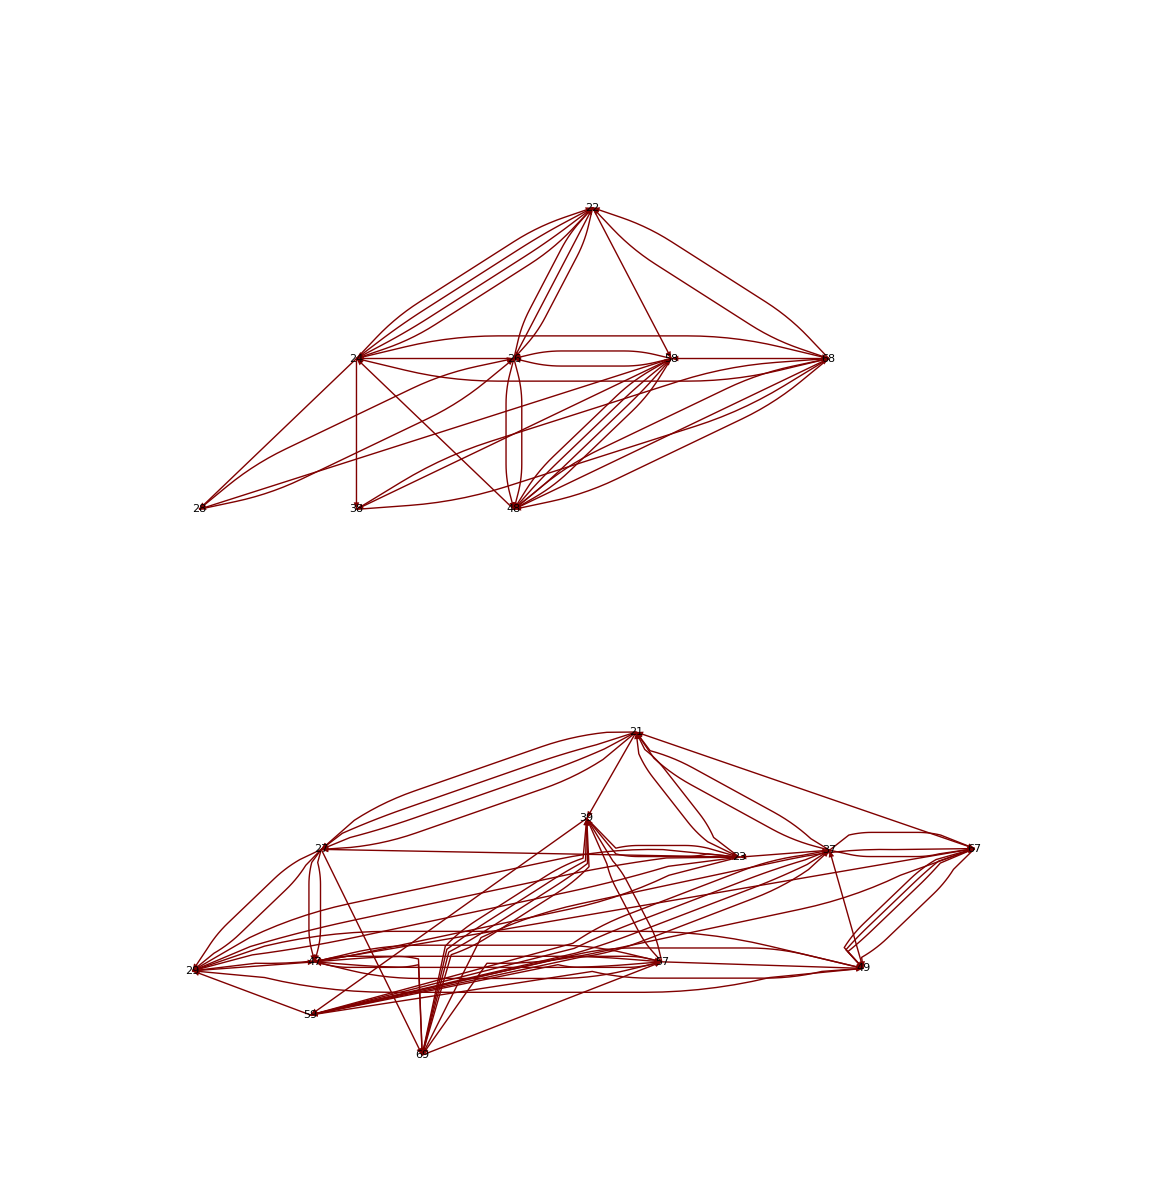

```mathematica
IT10=Exch[{StartSet,StartSet/.T10/.T10/.T10/.T10/.T10}]
```

{21→37,22→68,23→39,24→22,26→58,27→21,29→23,37→59,39→69,47→27,48→26,49→29,57→47,58→48,59→57,67→49,68→24,69→67}

```mathematica
T19=Exch[{StartSet,StartSet/.IT10/.T16/.S3}]
T17=Exch[{StartSet,StartSet/.T10/.IS3}]
T18=Exch[{StartSet,StartSet/.T15/.IS3}]
T20=Exch[{StartSet,StartSet/.T14/.IS3}]
T21=Exch[{StartSet,StartSet/.IT10/.S3/.T16}]
```

{22→38,23→37,24→22,26→58,27→69,28→26,37→23,38→68,48→28,49→57,57→49,58→48,68→24,69→27}

{23→27,24→38,26→68,27→69,28→24,29→67,37→23,38→58,39→29,49→37,57→49,58→28,67→39,68→26,69→57}

{23→27,24→38,26→68,27→69,28→24,29→67,37→23,38→58,39→29,49→37,57→49,58→28,67→39,68→26,69→57}

{22→48,24→58,48→22,58→24}

{22→68,23→57,24→22,26→38,27→69,28→24,29→39,37→23,38→58,39→67,48→26,49→27,57→49,58→48,67→29,68→28,69→37}

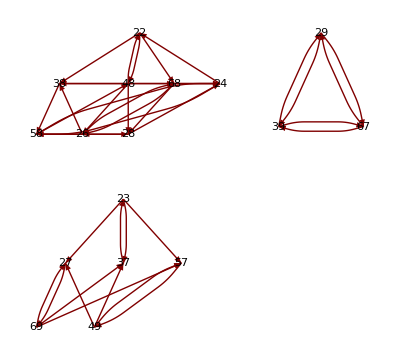

```mathematica
TreePlot[T20∪T17∪T18∪T19∪T21,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
S3,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,
T14=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1
T15=S6^-1 S3 S9^-1 S3^-1 S9 S6
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66不动的完备系,21到任意位置*)

S3,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,
T14=S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S3^2 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S3^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S2 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S7 S3^-1 S7^2 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3^-1 S8 S4^-1 S1 S9^-1 S1^-1 S2^2 S8 S4^-1 S1 S9^-1 S1^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S3 S1 S9 S1^-1 S4 S8^-1 S2^2 S1 S9 S1^-1 S4 S8^-1 S7^2 S3 S7^-1 S2^-1
T15=S6^-1 S3 S9^-1 S3^-1 S9 S6
(*保持11,41,53,12,42,13,43,63,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66不动的完备系,21到任意位置*)
```

```mathematica
Sl1={{11->17,"S1"},{17->19,"S1"},{19->13,"S1"},{13->11,"S1"},{14->18,"S1"},{18->16,"S1"},{16->12,"S1"},{12->14,"S1"},{31->61,"S1"},{61->43,"S1"},{43->53,"S1"},{53->31,"S1"},{33->63,"S1"},{63->41,"S1"},{41->51,"S1"},{51->33,"S1"},{32->62,"S1"},{62->42,"S1"},{42->52,"S1"},{52->32,"S1"}};
Sl2={{34->64,"S2"},{64->46,"S2"},{46->56,"S2"},{56->34,"S2"},{35->65,"S2"},{65->45,"S2"},{45->55,"S2"},{55->35,"S2"},{36->66,"S2"},{66->44,"S2"},{44->54,"S2"},{54->36,"S2"}};
Sl3={{21->27,"S3"},{27->29,"S3"},{29->23,"S3"},{23->21,"S3"},{24->28,"S3"},{28->26,"S3"},{26->22,"S3"},{22->24,"S3"},{37->67,"S3"},{67->49,"S3"},{49->59,"S3"},{59->37,"S3"},{39->69,"S3"},{69->47,"S3"},{47->57,"S3"},{57->39,"S3"},{38->68,"S3"},{68->48,"S3"},{48->58,"S3"},{58->38,"S3"}};
Sl4={{51->57,"S4"},{57->59,"S4"},{59->53,"S4"},{53->51,"S4"},{54->58,"S4"},{58->56,"S4"},{56->52,"S4"},{52->54,"S4"},{11->31,"S4"},{31->27,"S4"},{27->47,"S4"},{47->11,"S4"},{17->37,"S4"},{37->21,"S4"},{21->41,"S4"},{41->17,"S4"},{14->34,"S4"},{34->24,"S4"},{24->44,"S4"},{44->14,"S4"}};
Sl5={{12->32,"S5"},{32->28,"S5"},{28->48,"S5"},{48->12,"S5"},{18->38,"S5"},{38->22,"S5"},{22->42,"S5"},{42->18,"S5"},{15->35,"S5"},{35->25,"S5"},{25->45,"S5"},{45->15,"S5"}};
Sl6={{61->67,"S6"},{67->69,"S6"},{69->63,"S6"},{63->61,"S6"},{64->68,"S6"},{68->66,"S6"},{66->62,"S6"},{62->64,"S6"},{13->33,"S6"},{33->29,"S6"},{29->49,"S6"},{49->13,"S6"},{19->39,"S6"},{39->23,"S6"},{23->43,"S6"},{43->19,"S6"},{16->36,"S6"},{36->26,"S6"},{26->46,"S6"},{46->16,"S6"}};
Sl7={{31->33,"S7"},{33->39,"S7"},{39->37,"S7"},{37->31,"S7"},{32->36,"S7"},{36->38,"S7"},{38->34,"S7"},{34->32,"S7"},{17->61,"S7"},{61->29,"S7"},{29->57,"S7"},{57->17,"S7"},{19->67,"S7"},{67->27,"S7"},{27->51,"S7"},{51->19,"S7"},{18->64,"S7"},{64->28,"S7"},{28->54,"S7"},{54->18,"S7"}};
Sl8={{14->62,"S8"},{62->26,"S8"},{26->58,"S8"},{58->14,"S8"},{16->68,"S8"},{68->24,"S8"},{24->52,"S8"},{52->16,"S8"},{15->65,"S8"},{65->25,"S8"},{25->55,"S8"},{55->15,"S8"}};
Sl9={{41->43,"S9"},{43->49,"S9"},{49->47,"S9"},{47->41,"S9"},{42->46,"S9"},{46->48,"S9"},{48->44,"S9"},{44->42,"S9"},{11->63,"S9"},{63->23,"S9"},{23->59,"S9"},{59->11,"S9"},{13->69,"S9"},{69->21,"S9"},{21->53,"S9"},{53->13,"S9"},{12->66,"S9"},{66->22,"S9"},{22->56,"S9"},{56->12,"S9"}};
```